```mathematica
trueFull[ρ_,z_]:=ρ(HeavisideTheta[ρ-(2z-z^2)]((-12(6-6 √(1-ρ)+ρ(5 √(1-ρ)-8+2ρ)))/(ρ^3(1-ρ))-(2(6-6 √(1-ρ)-ρ(5-4 √(1-ρ))))/(ρ^2(1-ρ))Log[ρ/(2+2 √(1-ρ)-3ρ)])
+HeavisideTheta[2z-z^2-ρ]((12(1-2z)(2-2 √(1-ρ)-ρ)^2)/(ρ^3(2-2 √(1-ρ)-ρ(2-√(1-ρ))))-(2(6-6 √(1-ρ)-ρ(5-4 √(1-ρ))))/(ρ^2(1-ρ))Log[(2-4z(1-z-√(1-ρ))-2 √(1-ρ)-ρ)/(4z(1-z)-ρ)]))
trueSoft[ρ_,z_]:=HeavisideTheta[ρ-2z](-3-4Log[ρ/2]+4Log[2])+HeavisideTheta[2z-ρ](-3-4Log[z]-4Log[1-ρ/(4z)])
```

## Soft limit

```mathematica
Reduce[{Q z-(Q ρ)/4<(Q ρ)/4,Q>0},ρ]
```

z∈ℝ&&Q>0&&ρ>2 z

```mathematica
f[x_]:=ρ-(Q x)/4
Solve[f[kp]==0,kp]
```

{{kp→(4 ρ)/Q}}

```mathematica
f'[(4ρ)/Q]
```

-Q/4

```mathematica
Assuming[0<ρ<1,Integrate[DiracDelta[ρ-4x],{x,-1,2}]]
```

1/4

```mathematica
greaterIntegral=Assuming[{ϵ>0,Q ρ>0,0<ρ<1},Integrate[1/k^(1+ϵ),{k,(Q ρ)/4,Q-(Q ρ)/□}]]
lessIntegral=Assuming[{ϵ>0,Q ρ>0,ρ<2z,Q>0,0<z<1},Integrate[1/k^(1+ϵ),{k,Q z-(Q ρ)/4,Infinity}]]
```

(4^ϵ (Q ρ)^-ϵ)/ϵ

(Q (z-ρ/4))^-ϵ/ϵ

```mathematica
greaterPortion=FullSimplify[Series[(4Pi)^ϵ/(16 Pi^(5/2)Gamma[1/2-ϵ])8/Q 4^(1+ϵ)/(Q ρ)^(1+ϵ)greaterIntegral,{ϵ,0,0}]]
lessPortion=FullSimplify[Series[(4Pi)^ϵ/(16 Pi^(5/2)Gamma[1/2-ϵ])8/Q 4^(1+ϵ)/(Q ρ)^(1+ϵ)lessIntegral,{ϵ,0,0}]]
```

2/(π^3 Q^2 ρ ϵ)-(2 (EulerGamma-Log[16 π]+2 Log[Q ρ]))/(π^3 Q^2 ρ)+O[ϵ]^1

2/(π^3 Q^2 ρ ϵ)-(2 (EulerGamma-Log[16 π]+Log[Q (4 z-ρ)]+Log[Q ρ]))/(π^3 Q^2 ρ)+O[ϵ]^1

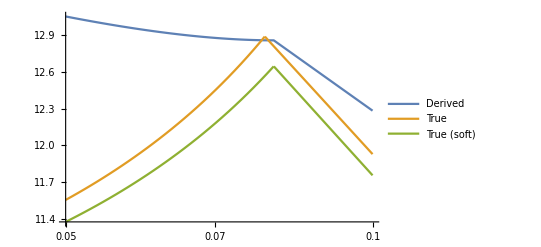

```mathematica
LogLinearPlot[ {20 ρ (HeavisideTheta[ρ-2z]Normal[greaterPortion]+HeavisideTheta[2z-ρ]Normal[lessPortion])/.{ϵ->1,Q->1,z->0.04},trueFull[ρ,0.04],trueSoft[ρ,0.04]},{ρ,0.05,0.1},PlotLegends->{ "Derived","True", "True (soft)"}]
```

## Attempt 2

```mathematica
FullSimplify[(2 Pi^((d-3)/2))/Gamma[(d-3)/2](dkp dkm)/(2Pi)^(d-1)(kp km)^((d-3)/2)1/(2 √(kp km))/.{d->4-2ϵ}]
```

(2^(-3+2 ϵ) dkm dkp (km kp)^-ϵ π^(-5/2+ϵ))/Gamma[1/2-ϵ]

```mathematica
Reduce[{Q>0,0≤z<1/2,Q z-(Q ρ)/4>(Q ρ)/4},ρ]
```

Q>0&&0≤z<1/2&&ρ<2 z

```mathematica
i1=Assuming[{ϵ>0,Q>0,0<ρ<1},Integrate[1/k^(1+ϵ),{k,Q ρ/4,Q}]]
i2=Assuming[{ϵ>0,Q>0,0<ρ<1,0≤z<1/2,ρ<2z},Integrate[1/k^(1+ϵ),{k,Q z-Q ρ/4,Q}]]
```

(-Q^-ϵ+4^ϵ (Q ρ)^-ϵ)/ϵ

(-Q^-ϵ+(Q (z-ρ/4))^-ϵ)/ϵ

```mathematica
fullSoln=Normal[Assuming[{Q>0,0≤z<1/2},FullSimplify[Series[4(4Pi)^ϵ/(8 Pi^(5/2)Gamma[1/2-ϵ])(4/Q)^ϵ 1/ρ^(1+ϵ)(HeavisideTheta[ρ-2z]i1+HeavisideTheta[2z-ρ]i2),{ϵ,0,0}]]]]
```

-(HeavisideTheta[2 z-ρ] Log[z-ρ/4]+HeavisideTheta[-2 z+ρ] Log[ρ/4])/(2 π^3 ρ)

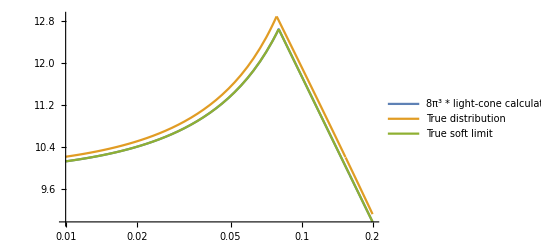

```mathematica
LogLinearPlot[{8Pi^3ρ fullSoln-3/.{z->0.04},trueFull[ρ,0.04],trueSoft[ρ,0.04]},{ρ,0.01,0.2},PlotLegends->{"8π^3 * light-cone calculation - 3", "True distribution", "True soft limit"}]
```

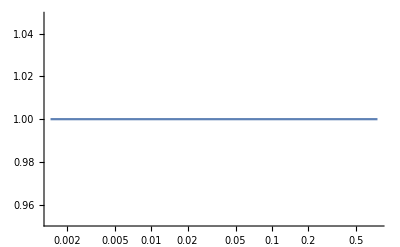

```mathematica
LogLinearPlot[{(trueSoft[ρ,0.04])/(8Pi^3ρ fullSoln-3/.{z->0.04})},{ρ,0.0,0.75}]
```

```mathematica
Assuming[{0<ρ<2z},FullSimplify[(trueSoft[ρ,z]+3)/(ρ fullSoln)]]
```

8 π^3

```mathematica
Assuming[{2z<ρ<1},FullSimplify[(trueSoft[ρ,z]+3)/(ρ fullSoln)]]
```

8 π^3

## Round 3

#### Before Laplace transforms

```mathematica
FullSimplify[Series[1/(8 Pi^(5/2)Gamma[1/2-ϵ])Q/2 4^(1+ϵ)/(Q ρ)^(1+ϵ)μ^(2ϵ)/ϵ(4/(Q ρ))^ϵ,{ϵ,0,0}]]
```

1/(4 π^3 ρ ϵ)-(EulerGamma-2 Log[μ]-Log[4/(Q ρ)]+Log[Q ρ])/(4 (π^3 ρ))+O[ϵ]^1

```mathematica
FullSimplify[Series[1/(8 Pi^(5/2)Gamma[1/2-ϵ])Q/2 4^(1+ϵ)/(Q ρ)^(1+ϵ)μ^(2ϵ)/ϵ(Q z-(Q ρ)/4)^-ϵ,{ϵ,0,0}]]
```

1/(4 π^3 ρ ϵ)-(EulerGamma-2 Log[μ]+Log[Q (z-ρ/4)]+Log[Q ρ])/(4 (π^3 ρ))+O[ϵ]^1

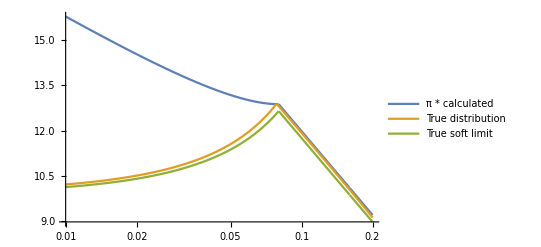

```mathematica
LogLinearPlot[{HeavisideTheta[ρ-0.08]2Log[4/ρ^2]-HeavisideTheta[0.08-ρ]2Log[ρ(0.04-ρ/4)],trueFull[ρ,0.04],trueSoft[ρ,0.04]},{ρ,0.01,0.2},PlotLegends->{"π * calculated", "True distribution", "True soft limit"}]
```

#### With Laplace transforms

We can transform the first term of our cross section fairly easily, but expanding the upper incomplete  gamma function as a series in ϵ seems difficult if we do  it directly:

```mathematica
FullSimplify[Series[Assuming[z>0,LaplaceTransform[HeavisideTheta[ρ-2z] 1/ρ^(1+2ϵ),ρ,ν]],{ϵ,0,2}]]
```

Gamma[0,2 z ν]+(2 Gamma[0,2 z ν] (Log[ν]-Log[2 z ν])-2 MeijerG[{{},{1,1}},{{0,0,0},{}},2 z ν]) ϵ+(2 Gamma[0,2 z ν] (Log[ν]-Log[2 z ν])^2+4 (-Log[ν]+Log[2 z ν]) MeijerG[{{},{1,1}},{{0,0,0},{}},2 z ν]+4 MeijerG[{{},{1,1,1}},{{0,0,0,0},{}},2 z ν]) ϵ^2+O[ϵ]^3

```mathematica
prefactor[ϵ_]:=1/(8 Pi^(5/2)Gamma[1/2-ϵ])Q/2(4/Q)^(1+2ϵ)μ^(2ϵ)/ϵ;
FullSimplify[Series[prefactor[ϵ] ν^(2 ϵ) Gamma[-2 ϵ,2 z ν],{ϵ,0,0}]]
```

Gamma[0,2 z ν]/(4 π^3 ϵ)+1/(4 π^3)(Gamma[0,2 z ν] (-EulerGamma+2 Log[1/Q]+2 Log[μ]+2 Log[ν]-2 Log[z ν])-2 MeijerG[{{},{1,1}},{{0,0,0},{}},2 z ν])+O[ϵ]^1

I  have absolutely no intuition about how to work with this Meijer G-function, even after looking it up (look how many parameters it has!), so let’s approach the problem obliquely.

```mathematica
part1=FullSimplify[Series[prefactor[ϵ] ν^(2ϵ)(Gamma[-2ϵ]),{ϵ,0,0}]]
```

-1/(8 π^3 ϵ^2)-(EulerGamma+Log[4]+2 Log[1/Q]+2 Log[μ]+2 Log[ν])/(8 π^3 ϵ)-1/(96 π^3)(π^2+6 (EulerGamma+Log[4])^2+24 (Log[1/Q]+Log[μ]+Log[ν]) (EulerGamma+Log[4]+Log[1/Q]+Log[μ]+Log[ν]))+O[ϵ]^1

```mathematica
part2=Assuming[0<z<1/2,FullSimplify[Series[prefactor[ϵ] ν^(2ϵ)Gamma[-2ϵ,0,2z],{ϵ,0,0}]]]
```

-1/(8 π^3 ϵ^2)-(EulerGamma+2 Gamma[0,2 z]+Log[4]+2 Log[1/Q]+2 Log[μ]+2 Log[ν])/(8 π^3 ϵ)+O[ϵ]^0

```mathematica
Integrate[((-1)^k t^(k+a-1))/(k!),{t,0,s}]
```

ConditionalExpression[((-1)^k s^(a+k))/((a+k) k!), Re[a+k]>0]

```mathematica
Sum[((-1)^k s^(a+k))/((a+k) k!),{k,0,2}]/.{a->-2ϵ}
```

-s^(1-2 ϵ)/(1-2 ϵ)+s^(2-2 ϵ)/(2 (2-2 ϵ))-s^(-2 ϵ)/(2 ϵ)

```mathematica
test1=Assuming[{0<z<1/2,Q>0,μ>0},FullSimplify[Series[prefactor[ϵ] ν^(2ϵ)(Gamma[-2ϵ]+(2z ν)^(-2ϵ)/(2ϵ)+(2z ν)^(1-2ϵ)/(1-2ϵ)+(2z ν)^(2-2ϵ)/(4(1-ϵ))),{ϵ,0,0}]]]
```

-(EulerGamma-z ν (2+z ν)+Log[2 z ν])/(4 π^3 ϵ)+1/(4 π^3)(-EulerGamma^2-π^2/6+Log[2]^2+Log[z]^2-z^2 ν^2 (-1+Log[4]+2 Log[z])-2 z^2 ν^2 Log[ν]+2 Log[z] Log[ν]+Log[ν]^2+Log[4] Log[z ν]-4 z ν (-1+Log[2 z ν])-(EulerGamma-z ν (2+z ν)+Log[2 z ν]) (-EulerGamma+Log[4]+2 Log[(μ ν)/Q]))+O[ϵ]^1

```mathematica
test3=FullSimplify[test1/.{z^b_/;b≥2->0,μ->Q}]
```

-(EulerGamma-z ν (2+z ν)+Log[2 z ν])/(4 π^3 ϵ)+1/(4 π^3)(-EulerGamma^2-π^2/6+Log[2]^2+Log[z]^2+2 Log[z] Log[ν]+Log[ν]^2+Log[4] Log[z ν]-4 z ν (-1+Log[2 z ν])-(-EulerGamma+Log[4]+2 Log[ν]) (EulerGamma-z ν (2+z ν)+Log[2 z ν]))+O[ϵ]^1

```mathematica
test2=Assuming[{0<z<1/2,Q>0,μ>0},FullSimplify[Series[prefactor[ϵ] ν^(2ϵ)(Gamma[-2ϵ]+(2z ν)^(-2ϵ)/(2ϵ)+(2z ν)^(1-2ϵ)/(1-2ϵ)),{ϵ,0,0}]]]
```

-(EulerGamma-2 z ν+Log[2 z ν])/(4 π^3 ϵ)+1/(4 π^3)(-EulerGamma^2-π^2/6+Log[2]^2+Log[z]^2+2 Log[z] Log[ν]+Log[ν]^2+Log[4] Log[z ν]-4 z ν (-1+Log[2 z ν])+(EulerGamma+Log[Q^2/(4 μ^2)]-2 Log[ν]) (EulerGamma-2 z ν+Log[2 z ν]))+O[ϵ]^1

```mathematica
Assuming[{z>0,Q==μ},FullSimplify[Normal[test3]-Normal[test2]]]
```

(z ν (2+z ν+ϵ (4-EulerGamma (2+z ν)+z ν Log[4])-4 ϵ Log[z]+2 z ϵ ν Log[ν]))/(4 π^3 ϵ)

```mathematica
Assuming[0<z<1/2,FullSimplify[Series[Gamma[-2ϵ]+(2z ν)^(-2ϵ)/(2ϵ)+(2z ν)^(1-2ϵ)/(1-2ϵ),{ϵ,0,2}]]]/.{EulerGamma->0}
```

(2 z ν-Log[2 z ν])+(-π^2/6+4 z ν+Log[2]^2+Log[z]^2+2 Log[z] Log[2 ν]+Log[ν] Log[4 ν]-4 z ν Log[2 z ν]) ϵ+(4 z ν Log[z ν] (-2+Log[4 z ν])+1/3 (12 z ν (2+Log[2]^2-Log[4])-2 Log[2 z ν]^3-4 Zeta[3])) ϵ^2+O[ϵ]^3

```mathematica
Assuming[{0<z<1/2},FullSimplify[4 Pi^3 Series[prefactor[ϵ] ν^(2ϵ)(Gamma[-2ϵ]+(2z ν)^(-2ϵ)/(2ϵ)+(2z ν)^(1-2ϵ)/(1-2ϵ)),{ϵ,0,0}]]/.{EulerGamma->0}]
```

(2 z ν-Log[2 z ν])/ϵ+(-π^2/6+Log[2]^2+Log[z]^2+2 Log[z] Log[ν]+Log[ν]^2+Log[4] Log[z ν]-4 z ν (-1+Log[2 z ν])+(-Log[4]-2 Log[1/Q]-2 Log[μ]-2 Log[ν]) (-2 z ν+Log[2 z ν]))+O[ϵ]^1

## Round 4

This time with plus functions

```mathematica
Assuming[(*{Q>0,μ>0,0<z<1/2,ρ>0}*),FullSimplify[Series[μ^(2ϵ)/Gamma[1/2-ϵ](4/Q)^(1+ϵ)1/ϵ(Q z-(Q ρ)/4)^-ϵ,{ϵ,0,1}]]/.{EulerGamma->0}]
```

4/(√π Q ϵ)-(4 (-Log[1/Q]-2 Log[μ]+Log[Q (z-ρ/4)]))/(√π Q)+((-π^2+2 (Log[1/Q]+2 Log[μ]-Log[Q (z-ρ/4)])^2) ϵ)/(√π Q)+O[ϵ]^2

```mathematica
LaplaceTransform[DiracDelta[ρ],ρ,ν]
```

1

```mathematica
LaplaceTransform[DiracDelta[ρ]Log[Q^2/μ^2(z-ρ/4)],ρ,ν]
```

Log[(Q^2 z)/μ^2]

```mathematica
Assuming[{(*Re[ν]>0,*)0<z<1/2},Integrate[Exp[-ρ ν]/ρ,{ρ,2z,1}]]
```

ExpIntegralEi[-ν]-ExpIntegralEi[-2 z ν]

```mathematica
Assuming[{Re[ν]>0,0<z<1/2},Integrate[(Exp[-ρ ν]-1)/ρ,{ρ,0,1}]]/.EulerGamma->0
```

-Gamma[0,ν]-Log[ν]

```mathematica
Integrate[(Exp[-ρ ν]-1)/ρ,ρ]
```

ExpIntegralEi[-ν ρ]-Log[ρ]

```mathematica
Assuming[0<z<1/2,LaplaceTransform[HeavisideTheta[2z-ρ]/ρ,ρ,ν]]
```

-EulerGamma+ExpIntegralEi[-2 z ν]-Log[ν]

```mathematica
Assuming[Re[ν]>0,FullSimplify[1/2(Log[-ν]-Log[-1/ν])==Log[ν]]]
```

Log[-1/ν]+2 Log[ν]==Log[-ν]

```mathematica
FullSimplify[Integrate[Log[ρ]/ρ(Exp[-ρ ν]-1),ρ]/.EulerGamma->0]
```

ν ρ HypergeometricPFQ[{1,1,1},{2,2,2},-ν ρ]-Log[ρ] (Gamma[0,ν ρ]+Log[ν ρ])

```mathematica
FullSimplify[Integrate[Log[ρ]/ρ(Exp[-ρ ν]-1),{ρ,0,1}]/.EulerGamma->0]
```

ν HypergeometricPFQ[{1,1,1},{2,2,2},-ν]

```mathematica
Assuming[{ρ>0,Re[ν]>0,0<z<1/2},FullSimplify[Integrate[Log[ρ]/ρ Exp[-ρ ν],ρ]/.EulerGamma->0]]
```

1/2 (2+2 ν ρ HypergeometricPFQ[{1,1,1},{2,2,2},-ν ρ]+Log[-1/ν]-Log[-ν]-Log[ρ] (2 (Gamma[0,ν ρ]+Log[ν])+Log[ρ]))

```mathematica
Assuming[{ρ>0,Re[ν]>0,0<z<1/2},FullSimplify[Integrate[Log[ρ]/ρ Exp[-ρ ν],{ρ,2z,1}]/.EulerGamma->0]]
```

Gamma[0,2 z ν] Log[2 z]-MeijerG[{{},{1,1}},{{0,0,0},{}},ν]+MeijerG[{{},{1,1}},{{0,0,0},{}},2 z ν]

#### Term 3

```mathematica
Integrate[1/ρ(Log[Q^2/μ^2(z-ρ/4)]Exp[-ρ ν]-Log[Q^2/μ^2 z]),{ρ,0,1}]
```

∫_0^1 (-Log[(Q^2 z)/μ^2]+ⅇ^(-ν ρ) Log[(Q^2 (z-ρ/4))/μ^2])/ρ ⅆρ

```mathematica
Assuming[0<z<1/2,Integrate[(Log[z-ρ/4]Exp[-ρ ν]-Log[z])/ρ,{ρ,0,1}]]
```

∫_0^1 (-Log[z]+ⅇ^(-ν ρ) Log[z-ρ/4])/ρ ⅆρ

```mathematica
Integrate[1/ρ(Log[Q^2/μ^2(z-ρ/4)]Exp[-ρ ν]),{ρ,2z,1}]
```

∫_(2 z)^1 (ⅇ^(-ν ρ) Log[(Q^2 (z-ρ/4))/μ^2])/ρ ⅆρ

```mathematica
D[Log[Q^2/μ^2(z-ρ/4)]^2,ρ]
```

-Log[(Q^2 (z-ρ/4))/μ^2]/(2 (z-ρ/4))

```mathematica
ComplexPlot[NIntegrate[1/ρ(Log[Q^2/μ^2(z-ρ/4)]Exp[-ρ ν]-Log[Q^2/μ^2 z])/.{z->0.04,Q->1,μ->1,ν->νval},{ρ,0,1}],{νval,-1-I,1+I}]
```

-Graphics-

```mathematica
NIntegrate[1/ρ(Log[Q^2/μ^2(z-ρ/4)]Exp[-ρ ν]-Log[Q^2/μ^2 z])/.{z->0.04,Q->1,μ->1,ν->1},{ρ,0,1}]
```

0.911468+3.73784 ⅈ

```mathematica
Integrate[Exp[-ρ ν]/ρ Log[Q^2/μ^2(z-ρ/4)],{ρ,2z,1}]
```

∫_(2 z)^1 (ⅇ^(-ν ρ) Log[(Q^2 (z-ρ/4))/μ^2])/ρ ⅆρ